## Graphics

```mathematica
RepeatableGraphics[x_,y_,size_]:=(*function to create a graphic of one segment of the tesselation(dodecagon and surrounding hexagons and squares), given an {x,y} coordinate for the segment's center and the size of the whole board*)
Module[
{offsetX=2.19x,offsetY=2.53834y+((2.53834/2)Abs[x]),colorLst=If[board=={},Table[LightGray,{i,1,13}],If[TrueQ@showMines,colorMineLst[{x,y},size],colorFlagLst[{x,y},size]]]},
{(*all of the hard coded values are relative values for placement of shapes in a single segment, they don't need to be changed*)
(*central dodecagon*)
EdgeForm[Thick],colorLst[[1]],RegularPolygon[{offsetX,offsetY},1.04,12],
(*All of the surrounding shapes in clockwise order*)
colorLst[[2]],RegularPolygon[{offsetX,offsetY+1+(.538344/2)},.761333/2,4],
colorLst[[3]],RegularPolygon[{offsetX+.73,offsetY+1+.538344/2},{.53,π/2},6],
colorLst[[4]],RegularPolygon[{offsetX+1.095,offsetY+0.634586},{.380667,-π/12},4],
colorLst[[5]],RegularPolygon[{offsetX+1.46,offsetY},{.53,π/2},6],
colorLst[[6]],RegularPolygon[{offsetX+1.095,offsetY-0.634586},{.380667,π/12},4],
colorLst[[7]],RegularPolygon[{offsetX+.73,offsetY-1-.538344/2},{.53,π/2},6],
colorLst[[8]],RegularPolygon[{offsetX,offsetY-1-(.538344/2)},.761333/2,4],
colorLst[[9]],RegularPolygon[{offsetX-.73,offsetY-1-.538344/2},{.53,π/2},6],
colorLst[[10]],RegularPolygon[{offsetX-1.095,offsetY-0.634586},{.380667,-π/12},4],
colorLst[[11]],RegularPolygon[{offsetX-1.46,offsetY},{.53,π/2},6],
colorLst[[12]],RegularPolygon[{offsetX-1.095,offsetY+0.634586},{.380667,π/12},4],
colorLst[[13]],RegularPolygon[{offsetX-.73,offsetY+1+.538344/2},{.53,π/2},6]
}
]
```

```mathematica
textLst[x_,y_,size_]:=Module[(*creates a list of text objects and their coordinates if the tile they are in has been opened, and if so, also attributes a color to the number such that 1 is blue, 2 is gree, 3 is red, 4 is crimson*)
{polar=polarConv[{x,y},size],coordLst,graphicsLst={},font=fontSize[size],(*this list holds all the local coordinates for the center of tiles in a RepeatableGraphics*)locLst={{0,0},{0,1+.538344/2},{.73,1+.538344/2},{1.095,.634586},{1.46,0},{1.095,-.634586},{.73,-1-.538344/2},{0,-1-.538344/2},{-.73,-1-.538344/2},{-1.095,-.634586},{-1.46,0},{-1.095,.634586},{-.73,1+.538344/2}},
offsetX=2.19x,offsetY=2.53834y+((2.53834/2)Abs[x])},
coordLst=Prepend[northMostTile[{x,y},size],polar];
Table[(*adds only the numbers and coordinates of tiles that are open (meaning they are not 'unknown' tiles, the player has determined them to be not mines)*)If[getNum[board[[coordLst[[i,1]],coordLst[[i,2]]]]]≠0&&TrueQ[getOpen[board[[coordLst[[i,1]],coordLst[[i,2]]]]]],AppendTo[graphicsLst,
{
Switch[getNum[board[[coordLst[[i,1]],coordLst[[i,2]]]]],
1,Blue,
2,Green,
3,Red,
_,Darker[Red]
],
If[!TrueQ@getMine[board[[coordLst[[i,1]],coordLst[[i,2]]]]],Text[Style[getNum[board[[coordLst[[i,1]],coordLst[[i,2]]]]],font],{offsetX+locLst[[i,1]],offsetY+locLst[[i,2]]}]]}]];,{i,1,13}];
Return[graphicsLst]
]
```

```mathematica
colorFlagLst[{x_,y_},size_]:=Module[(*creates a list that specifies the color of each tile in a RepeatableGraphics section, LightGray if the tile has not been clicked, White if it has been clicked to open to see the number, and Red if the tile was marked as a flag*)
{polar=polarConv[{x,y},size],coordLst},
coordLst=Prepend[northMostTile[{x,y},size],polar];
Table[If[getFlag[board[[coordLst[[i,1]],coordLst[[i,2]]]]],Red,If[!getOpen[board[[coordLst[[i,1]],coordLst[[i,2]]]]],LightGray,White]],{i,1,13}]
]
```

```mathematica
colorMineLst[{x_,y_},size_]:=Module[(*creates a list that specifies the color of each mine in a RepeatableGraphics section as black when the game is lost*)
{polar=polarConv[{x,y},size],coordLst},
coordLst=Prepend[northMostTile[{x,y},size],polar];
Table[If[TrueQ@getMine[board[[coordLst[[i,1]],coordLst[[i,2]]]]],Black,If[getFlag[board[[coordLst[[i,1]],coordLst[[i,2]]]]],Red,If[!getOpen[board[[coordLst[[i,1]],coordLst[[i,2]]]]],LightGray,White]]],{i,1,13}]
]
```

```mathematica
boardOfSize[size_]:=Module[(*creates a board of a given size, where size is the number of RepeatableGraphics along a side of the board*)
{tiles={},numbers={}},
Table[Table[
AppendTo[tiles,RepeatableGraphics[k,j,size]];(*The tiles for the board are created here*)
If[board≠{},AppendTo[numbers,textLst[k,j,size]]];,{j,0-(size-1),((2*size)-2)-Abs[k]-(size-1)}],(*the numbers to be displayed in the tiles are created here*)
{k,0-(size-1),size-1}];
Return[AppendTo[tiles,numbers]]
]
```

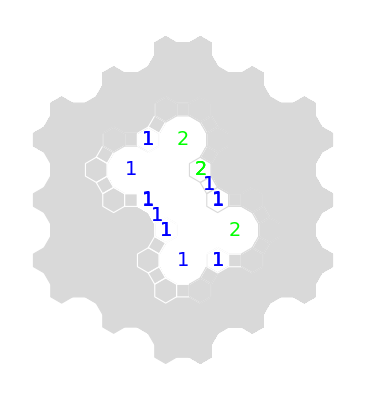

```mathematica
Graphics@boardOfSize[3]
```

### Beginner: size 3 Intermediate: size 4 Expert: size 5 Custom: size N

### Size 3 ---> FontSize 20 Size 4 ---> FontSize 15 Size 5 ---> FontSize 10 Size 7 ---> FontSize 9 Size 9 ---> FontSize 7 font size is always the same no matter the graphic size so the larger the board, the smaller the font size needs to be

```mathematica
fontSize[x_]=Fit[{{3,20},{4,15},{5,10},{7,9},{9,7}},{1,x^-1},x];(*parameter x is size of board*)
```

```mathematica
fontSize[8]
```

7.37113

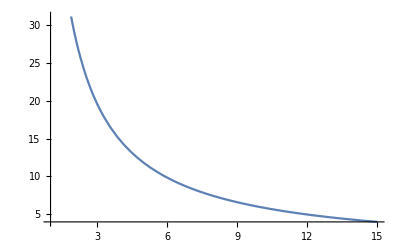

```mathematica
Plot[Out[949],{x,1,15}]
```

## Border Detection

```mathematica
(* given a set of coordinates, this calculates the coordinates of the adjacent tiles. *)
surrounding[coord_]:=
If[OddQ[coord[[1]]*coord[[2]]],surroundingDodec@coord,
If[OddQ[coord[[1]]+coord[[2]]],surroundingSquare@coord,
surroundingHex@coord]]
```

## surroundingDodec

```mathematica
(* gives the coordinates of all tiles surrounding a given dodecagon. *)
surroundingDodec[coord_]:=Module[{result},
If[coord=={1,1},result=Table[{2,x},{x,12}], (* Handles the {1,1} special case. *)
If[Mod[coord[[2]]-1,coord[[1]]-1]==0,result=sDodecCorner@coord,(* Handles the case in which the dodecagon is on a corner. *)
result=sDodecSide@coord] (* Handles the case in which the dodecagon is on a side*)
];
Return[result]
]
```

```mathematica
(* handles the case in which the dodecagon is on a corner. *)
sDodecCorner[coord_]:=Module[
{innerCenter={coord[[1]]-1,2*Floor[coord[[2]]/(coord[[1]]-1)]*(coord[[1]]-2)+1}, (* Finds the center tile on the inner edge of the dodecagon. *)
outerCenter={coord[[1]]+1,2*Floor[coord[[2]]/(coord[[1]]-1)]*coord[[1]]+1}},(* Finds the center tile on the outer edge of the dodecagon. *)
Return@Flatten[
{{{coord[[1]],Mod[coord[[2]]-1,6*coord[[1]]-6,1]}},
Table[{outerCenter[[1]],Mod[outerCenter[[2]]+n,12*outerCenter[[1]]-12,1]},{n,-3,3}],
(* All tiles on the outer edge. *)
{{coord[[1]],Mod[coord[[2]]+1,6*coord[[1]]-6,1]}},
Table[{innerCenter[[1]],Mod[innerCenter[[2]]+n,12*innerCenter[[1]]-12,1]},{n,1,-1,-1}]
(* All tiles on the inner edge. *)
},1]
]
```

```mathematica
(* handles the case in which the dodecagon is on a side. *)
sDodecSide[coord_]:=Module[
{innerCenter={coord[[1]]-1,Floor[coord[[2]]/(coord[[1]]-1)]*2*(coord[[1]]-2)+2*Mod[coord[[2]],coord[[1]]-1]-2},(* Finds the center tile on the inner edge of the dodecagon. *)
outerCenter={coord[[1]]+1,Floor[coord[[2]]/(coord[[1]]-1)]*2*coord[[1]]+2*Mod[coord[[2]],coord[[1]]-1]}
(* Finds the center tile on the outer edge of the dodecagon. *)
},
Return@Flatten[{
{{coord[[1]],Mod[coord[[2]]-1,6*coord[[1]]-6,1]}},
Table[{outerCenter[[1]],Mod[outerCenter[[2]]+n,12*outerCenter[[1]]-12,1]},{n,-2,2}],
(* All tiles on the outer edge. *)
{{coord[[1]],Mod[coord[[2]]+1,6*coord[[1]]-6,1]}},
Table[{innerCenter[[1]],Mod[innerCenter[[2]]+n,12*innerCenter[[1]]-12,1]},{n,2,-2,-1}](* Both tiles adjacent in the row. *)
},1]
]
```

```mathematica
surroundingDodec[{5,7}]
```

{{5,6},{6,14},{6,15},{6,16},{6,17},{6,18},{5,8},{4,8},{4,9},{4,10},{4,11},{4,12}}

## surroundingHex

```mathematica
(* gives all coordinates adjacent to the given hexagon *)
surroundingHex[coord_]:=
Flatten[{{{coord[[1]],Mod[coord[[2]]-1,rowLength[coord[[1]]],1]}},
If[outOrIn@coord==1,hexSquare@coord,{hexDodec@coord}],
{{coord[[1]],Mod[coord[[2]]+1,rowLength[coord[[1]]],1]}}, (* both tiles adjacent in the row *)
If[outOrIn@coord==-1,hexSquare@coord,{hexDodec@coord}]
},
1]
```

```mathematica
(* finds the dodecagon adjacent in the row above or below, depending on the hex's position. *)
hexDodec[coord_]:=Module[{row = coord[[1]]-outOrIn@coord,cnt},
For[cnt=1,cnt<=rowLength@row,cnt+=2,
If[Length@Select[surroundingDodec@{row,cnt},#==coord&]==1, 
Return[{row,Mod[cnt,rowLength[row],1]}]]
];
]
```

```mathematica
(* finds the adjacent set of dodecagon-square-dodecagon in the row above or below, depending on the hex's position. *)
hexSquare[coord_]:=Module[{row=coord[[1]]+outOrIn@coord,cnt},
For[cnt=1,cnt<=rowLength@row,cnt+=2,
If[Length@Select[surroundingDodec@{row,cnt},#==coord&]==1&&Length@Select[surroundingDodec@{row,cnt+2},#==coord&]==1,Return[Table[{row, Mod[cnt+a, rowLength[row],1]},{a,0,2}]]]
];
]
```

```mathematica
(* determines the hex's position: if the lone dodecagon is in the row above (out) or the row below (in). *)
outOrIn[coord_]:=If[OddQ[Mod[coord[[2]]/2,(coord[[1]]-1),1]],1,-1]
```

```mathematica
(* calculates the length of a given row. *)
rowLength[row_]:=If[row==1,1,If[OddQ[row],(row-1)*6,(row-1)*12]]
```

```mathematica
surroundingHex[{2,10}]
```

{{2,9},{3,9},{3,10},{3,11},{2,11},{1,1}}

## surroundingSquare

```mathematica
(* gives all coordinates adjacent to the given square *)
surroundingSquare[coord_]:=
Flatten[{{{coord[[1]],Mod[coord[[2]]+1,rowLength[coord[[1]]],1]}},
{If[EvenQ[coord[[1]]],squareDodecs@coord,squareHexes@coord][[1]]},
{{coord[[1]],Mod[coord[[2]]-1,rowLength[coord[[1]]],1]}},
{If[EvenQ[coord[[1]]],squareDodecs@coord,squareHexes@coord][[2]]}},1]
```

```mathematica
surroundingSquare[{2,5}]
```

{{2,6},{1,1},{2,4},{3,5}}

```mathematica
(* handles the case in which the bordering tiles in the adjacent rows are dodecagons. *)
squareDodecs[coord_] := Module[{row=coord[[1]],cnt,coord1,coord2},
For[cnt=1,cnt<=rowLength@(row-1),cnt+=2,
If[Length@Select[surroundingDodec@{row-1,cnt},#==coord&]==1,
coord1={row-1,Mod[cnt,rowLength[row-1],1]};Break]
];
For[cnt=1,cnt<=rowLength@(row+1),cnt+=2,
If[Length@Select[surroundingDodec@{row+1,cnt},#==coord&]==1,
coord2={row+1,Mod[cnt,rowLength[row+1],1]};Break]
];
Return[{coord1,coord2}]
]
```

```mathematica
(* handles the case in which the bordering tiles in the adjacent rows are hexagons. *)
squareHexes[coord_] :=  Module[{row=coord[[1]],cnt,coord1,coord2},
For[cnt=2,cnt<=rowLength@(row-1),cnt+=2,
If[Length@Select[surroundingHex@{row-1,cnt},#==coord&]==1,
coord1={row-1,Mod[cnt,rowLength[row-1],1]};Break]
];
For[cnt=2,cnt<=rowLength@(row+1),cnt+=2,
If[Length@Select[surroundingHex@{row+1,cnt},#==coord&]==1,
coord2={row+1,Mod[cnt,rowLength[row+1],1]};Break]
];
Return[{coord1,coord2}]
]
```

```mathematica
surroundingSquare[{4,35}]
```

{{4,36},{4,34},{3,1},{5,23}}

## testing

```mathematica
surrounding[{1,1}]
```

{{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{2,11},{2,12}}

```mathematica
surrounding[{3,7}]
```

{{2,6},{2,7},{2,8},{4,16},{4,17},{4,18},{4,19},{4,20},{4,21},{4,22},{3,6},{3,8}}

```mathematica
surrounding[{4,5}]
```

{{4,6},{4,4},{3,3},{5,3}}

```mathematica
surrounding[{6,13}]
```

{{6,14},{6,12},{5,5},{7,9}}

```mathematica
surrounding[{4,2}]
```

{{4,3},{4,1},{3,1},{5,1},{5,2},{5,3}}

```mathematica
surrounding[{6,60}]
```

{{6,1},{6,59},{5,1},{7,35},{7,36},{7,1}}

## Board Generation

```mathematica
createTile[mine_,num_,flag_,open_]:={mine,num,flag,open}
```

```mathematica
getMine[tile_]:=tile[[1]]
```

```mathematica
getNum[tile_]:=tile[[2]]
```

```mathematica
getFlag[tile_]:=tile[[3]]
```

```mathematica
getOpen[tile_]:=tile[[4]]
```

```mathematica
(* creates a board of boardSize with a given number of mines, and an initial click which must be zero. *)
createBoard[boardSize_,mines_,init_]:=Module[{cnt1,cnt2,minespots,numbers},
showMines=False;

minespots=mineLocationGenerator[boardSize,mines,init];
numbers=Select[Flatten[Table[surrounding[minespot],{minespot,minespots}],1],#[[1]]≤boardSize*2&];
numbers=Table[Count[numbers,{x,y}],{x,boardSize*2},{y,rowLength[x]}];

board=Table[createTile[MemberQ[minespots,{x,y}],numbers[[x,y]],False,False],{x,boardSize*2},{y,rowLength[x]}];

Return[board]
]
```

```mathematica
(* generates mine locations given a number of mines, a board size, and an initial click which must be a zero. *)
mineLocationGenerator[boardSize_,mines_,init_]:=RandomSample[Select[Flatten[Table[{x,y},{x,boardSize*2},{y,rowLength[x]}],1],!MemberQ[Flatten[{{init},surrounding[init]},1],#]&],mines]
```

```mathematica
createBoard[3,30,{1,1}];
```

## Board Processing

```mathematica
(* checks if the game has been lost. if an open tile has a mine, returns True, otherwise, False.*)
gameLost[board_]:=Module[{flatBoard=Flatten[board,1]},
If[Length@Select[flatBoard,(getMine@#&&getOpen@#)&]>0,Return[True],Return[False]]
]
```

```mathematica
(* checks if the game has been won. if there exists a closed tile without a mine, returns False, otherwise, True.*)
gameWon[board_]:=Module[{flatBoard=Flatten[board,1]},
If[Length@Select[flatBoard,(!getMine@#&&!getOpen@#)&]>0,Return[False],Return[True]]
]
```

```mathematica
(* processes a click in a given location. *)
processClick[boardSize_,mines_,board_,coord_,type_]:=Module[{current,newBoard=If[board=={},createBoard[boardSize,mines,coord],board]},
If[gameLost[newBoard]||gameWon[newBoard],Return[newBoard]];
current=Part@@Flatten[{{newBoard},Flatten[{coord}]},1];
If[getOpen@current,Return[newBoard]];
If[type==1,
newBoard=ReplacePart[newBoard,Flatten[{coord,3}]->!getFlag@current],
If[!getFlag@current,
newBoard=ReplacePart[newBoard,Flatten[{coord,4}]->True];If[getNum@current== 0,Do[newBoard=processClick[boardSize,mines,newBoard,newCoord,type],{newCoord,Select[surrounding[coord],(#[[1]]≤boardSize*2)&]}]
]
]
];
If[gameLost[newBoard],newBoard=endGame[newBoard]];
Return[newBoard]
]
```

```mathematica
(* reveals all mine locations if the game is lost. *)
endGame[board_]:=Module[{finalBoard=board},
Do[If[getMine@board[[x,y]],
finalBoard=ReplacePart[finalBoard,{x,y,4}->True]],{x,Length@board},{y,rowLength@x}];
showMines=True;
Return[finalBoard]
]
```

```mathematica
bTest=processClick[5,80,{},{2,1},0]
```

## Conversion of Coordinates

```mathematica
centeredCoords[{x_,y_},size_]:=Module[(*takes the cartesian coordinates used in the graphics output and moves them to where they would be if the center of the board were at {0,0}*)
{xc=x-(size-1),yc=y-(size-1)},
If[yc≥0&&xc≠0,yc = yc+(Abs[xc])];
Return[{xc,yc}]
]
```

```mathematica
centeredCoords[{2,2},3]
```

{0,0}

```mathematica
polarRow[{x_,y_}]:=Max[Abs[x],Abs[y]]*2+1(*equation to determine what polar row of the board a cartesian coordinate is in.*)
```

```mathematica
polarCol[{x_,y_}]:=If[Abs[x]<=Abs[y],polarColHoriz[{x,y}],polarColVert[{x,y}]](*determines what index in a polar row that a cartesian coordinate has*)
```

```mathematica
polarColHoriz[{x_,y_}]:=Mod[1+If[Sign[y]==-1,rowLength[polarRow[{x,y}]]/2-2x,2x],rowLength[polarRow[{x,y}]],1]
```

```mathematica
polarColVert[{x_,y_}]:=polarColHoriz[{x,-Abs[x]}]-Sign[x]*2*(Abs[x]-Abs[y])
```

```mathematica
polarConv[{x_,y_},size_]:=Module[{yc},
If[y≥0&&x≠0,yc = y+(Abs[x]),yc=y];
Return[{polarRow[{x,yc}],polarCol[{x,yc}]}]
](*converts a cartesian coordinate into a polar tile index*)
```

```mathematica
polarConv[{-1,0},5]
```

{3,11}

### Determining the Cartesian and polar-like coordinates for which tile was clicked

```mathematica
regionShapes[x_,y_,size_]:=(*function to create a graphic of one segment of the tesselation(dodecagon and surrounding hexagons and squares), given an {x,y} coordinate for the segment's center and the size of the whole board*)
Module[
{offsetX=2.19x,offsetY=2.53834y+((2.53834/2)Abs[x])},
{(*all of the hard coded values are relative values for placement of shapes in a single segment, they don't need to be changed*)
(*central dodecagon*)
RegularPolygon[{offsetX,offsetY},1.04,12],
(*all of the surrounding shapes in clockwise order starting with the north-most shape*)
RegularPolygon[{offsetX,offsetY+1+(.538344/2)},.761333/2,4],
RegularPolygon[{offsetX+.73,offsetY+1+.538344/2},{.53,π/2},6],
RegularPolygon[{offsetX+1.095,offsetY+0.634586},{.380667,-π/12},4],
RegularPolygon[{offsetX+1.46,offsetY},{.53,π/2},6],
RegularPolygon[{offsetX+1.095,offsetY-0.634586},{.380667,π/12},4],
RegularPolygon[{offsetX+.73,offsetY-1-.538344/2},{.53,π/2},6],
RegularPolygon[{offsetX,offsetY-1-(.538344/2)},.761333/2,4],
RegularPolygon[{offsetX-.73,offsetY-1-.538344/2},{.53,π/2},6],
RegularPolygon[{offsetX-1.095,offsetY-0.634586},{.380667,-π/12},4],
RegularPolygon[{offsetX-1.46,offsetY},{.53,π/2},6],
RegularPolygon[{offsetX-1.095,offsetY+0.634586},{.380667,π/12},4],
RegularPolygon[{offsetX-.73,offsetY+1+.538344/2},{.53,π/2},6]
}
]
```

```mathematica
findTile[{x_,y_},size_]:=Module[
{shapeLoc},
Do[
Do[
If[
RegionDistance[Disk[{2.19k,2.53834j+((2.53834/2)Abs[k])},1.94163],{x,y}]==0,
Do[
If[
RegionDistance[
regionShapes[k,j,size][[i]],{x,y}]==0,
shapeLoc={{k,j},i};
Return[shapeLoc]
],{i,13}];
If[Length@shapeLoc==2,Break[]];
Do[
If[
RegionDistance[
regionShapes[k,j+1,size][[i]],{x,y}]==0,
shapeLoc={{k,j+1},i};
Return[shapeLoc]
],{i,13}];
If[Length@shapeLoc==2,Break[]];
Do[
If[
k≥0,
j++;];
Do[
If[
RegionDistance[
regionShapes[k+1,j+c,size][[i]],{x,y}]==0,
shapeLoc={{k+1,j+c},i};
Return[shapeLoc]
],{c,0,1}];If[Length@shapeLoc==2,Break[]];,{i,13}]];If[Length@shapeLoc==2,Break[]];,{j,0-(size-1),((2*size)-2)-Abs[k]-(size-1)}];If[Length@shapeLoc==2,Break[]];,
{k,0-(size-1),2*size-2-(size-1)}];
If[Length@shapeLoc==2,
Return[shapeLoc]]
]
```

```mathematica
northMostTile[{x_,y_},size_]:=Module[(*Gives the tiles surrounding a dodecagon in clockwise order starting from the northmost tile*)
{coord=polarConv[{x,y},size],rtnLst={},row,polarCol},
row=coord[[1]];polarCol=coord[[2]];
If[row==1,Return[surrounding[{1,1}]],(*if the given coordinate is the centermost dodecagon, the list returned by surrounding already starts on the northmost tile.*)
If[Mod[polarCol-1,(2*size-1)-(2*size-row)]==0,(*this equation determines if the dodecagon is a corner*)
Switch[(polarCol-1)/((2*size-1)-(2*size-row)),(*if it is, this equation gives a number 0 through 5 for which corner it is, and then we just use a Rotate function on the list given by surrounding function*)
0,Return[RotateLeft[surrounding[{row,polarCol}],4]],
1,Return[RotateLeft[surrounding[{row,polarCol}],2]],
2,Return[surrounding[{row,polarCol}]],
3,Return[RotateRight[surrounding[{row,polarCol}],2]],
4,Return[RotateRight[surrounding[{row,polarCol}],4]],
5,Return[RotateRight[surrounding[{row,polarCol}],6]]
],
Switch[Floor[(polarCol-1)/((2*size-1)-(2*size-row))],(*if it is not a corner, this function gives us a number 0 through 5 to determine which side it follows. We can use a Rotate function on surrounding function here as well.*)
0,Return[RotateLeft[surrounding[{row,polarCol}],2]],
1,Return[surrounding[{row,polarCol}]],
2,Return[RotateRight[surrounding[{row,polarCol}],2]],
3,Return[RotateRight[surrounding[{row,polarCol}],4]],
4,Return[RotateRight[surrounding[{row,polarCol}],6]],
5,Return[RotateRight[surrounding[{row,polarCol}],8]]
]
]
]
]
```

```mathematica
giveClickedTile[{x_,y_},size_]:=Module[(*for any coordinate clicked in the clickpane,will return the polar coordinate of the tile clicked,if the click was inside a tile*){tile=findTile[{x,y},size],coord},
If[Length@tile≠0,coord=tile[[1]];
Return[Prepend[northMostTile[coord,size],polarConv[coord,size]][[tile[[2]]]]],Null]]
```

```mathematica
giveClickedTile[{2,2.5},5]
```

{4,5}

## GUI

```mathematica
openingScreen[]:=Column@{
Graphics[Text[Style["Matheminesweeper!",Large,Red]],ImageSize->250, AspectRatio->2/3],
Button["New Game",screen=sizeSelect[]],
Button["Instructions",screen=instructions[]]
}
```

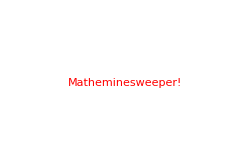
-Graphics-
New Game
Instructions

```mathematica
openingScreen[]
```

```mathematica
sizeSelect[]:= Column@{
Graphics[Text[Style["Select a Size",Medium]],ImageSize->100,AspectRatio->1/4],
Button["Beginner", globalSize=3;globalMines=20;screen=mainScreen[]],
Button["Intermediate", globalSize=4;globalMines=55;screen=mainScreen[]],
Button["Expert",globalSize=5;globalMines=90;screen=mainScreen[]]
}
```

```mathematica
sizeSelect[]
```

-Graphics-
Beginner
Intermediate
Expert

```mathematica
instructions[]:=Column@{
Graphics[Text[
Style["Click on a tile to open it. The numbers designate
 how many mines are adjacent to that tile. Toggle 
 between opening tiles and flagging them by clicking the 
 button labeled \"Open\" or \"Flag\" below the map. Open all 
non-mine tiles to win.",Medium]
],ImageSize->310,AspectRatio->1/3
],
Button["Back to Home Screen",screen=openingScreen[]]
}
```

```mathematica
instructions[]
```

-Graphics-
Back to Home Screen

```mathematica
mainScreen[]:=DynamicModule[{type=0,click=Null},
Column@{
ClickPane[
Dynamic@Graphics[boardOfSize[globalSize],ImageSize->Large],
(click=giveClickedTile[#,globalSize];
If[!(click===Null),
board=processClick[globalSize,globalMines,board,click,type]
])&
],
Row@{
Button["Back to home",screen=openingScreen[];board={}],
Button["Reset",board={}],
Button[Dynamic@If[type==0,"Open","Flag"],type=Mod[type+1,2]]
}
}
]
```

```mathematica
visualizeGame[]:=Module[
{},
screen=openingScreen[];
board={};
globalSize=3;
globalMines=30;
Dynamic[screen]
]
```

```mathematica
visualizeGame[]
```

```mathematica
playGame[]:=CreateWindow[PaletteNotebook[visualizeGame[],WindowSize->Fit,WindowTitle->"Matheminesweeper",WindowMargins->Automatic]]
```

## AI Work (Unfinished)

```mathematica
(* returns what a tile should display given its state. *)
display[tile_]:=
If[getOpen@tile,
If[getMine@tile,"mine",ToString@getNum@tile],
If[getFlag@tile,"flag","closed"]
]
```

```mathematica
displayBoard[board_]:=Module[{displayBoard=board},
Do[displayBoard=ReplacePart[displayBoard,{x,y}->display[board[[x,y]]]],{x,Length@board},{y,rowLength@x}];
Return[displayBoard]
]
```

```mathematica
displayBoard[processClick[3,15,{},{2,1},0]]
```

{{1},{0,0,0,0,1,closed,closed,closed,closed,closed,closed,1},{2,0,1,0,1,closed,closed,closed,closed,closed,closed,closed},{closed,closed,closed,1,closed,closed,closed,1,0,0,0,0,0,0,0,1,1,1,1,1,closed,closed,closed,closed,closed,1,closed,closed,closed,closed,closed,closed,closed,closed,closed,closed},{closed,closed,closed,closed,closed,closed,1,0,0,0,0,0,0,0,2,1,2,0,2,closed,closed,closed,closed,closed},{closed,closed,closed,closed,closed,closed,closed,closed,closed,closed,closed,closed,closed,closed,closed,closed,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,closed,closed,closed,closed,closed,closed,closed,closed,closed,closed,closed,closed,closed}}

```mathematica
tilesInSize[size_]:=Sum[rowLength[x],{x,size*2}]
```

```mathematica
randomBoard[size_,mines_]:=Module[{x=RandomInteger[{1,size*2}],y,init,progress,randomBoard,toOpen},
y=RandomInteger[{1,rowLength[x]}];init={x,y};
randomBoard=processClick[size,mines,{},init,0];
toOpen=Position[randomBoard,{False,_,_,False}];
progress=RandomInteger[{0,Length@toOpen}];
Do[randomBoard=processClick[size,mines,randomBoard,open,0],{open,RandomSample[toOpen,progress]}];
Return[randomBoard]
]
```

```mathematica
createAI[size_,mines_,boards_]:=Module[
{sampleBoards=Table[randomBoard[size,mines],boards],
boardDisplays, closedPositions,inputData,outputData},
boardDisplays=Table[displayBoard[sampleBoard],{sampleBoard,sampleBoards}];
closedPositions=Table[Position[boardDisplay,"closed"],{boardDisplay,boardDisplays}];
inputData=Flatten[Table[{closedPosition,boardDisplays[[i]]},{i,boards},{closedPosition,closedPositions[[i]]}],1];
outputData=Flatten[Table[!gameLost[processClick[size,mines,sampleBoards[[i]],tile,0]],{i,boards},{tile,closedPositions[[i]]}],1];
Return[Classify[inputData->outputData]]
]
```

## Play Game

```mathematica
(*to show that larger board sizes do work but we can't figure out why they don't generate when the game is running*)
globalMines=90;
globalSize=7;
board=processClick[globalSize,globalMines,{},{1,1},0];
```

$Aborted

```mathematica
playGame[]
```